```mathematica
(*The following is the quenched average of the partition function, to be used in the annaled approximation*)

Qmin= 1
Tmin = Exp[-α]
Hmin = Exp[-2α]
Qplus = Exp[-4α]
Tplus = Exp[-3α]
Hplus = Exp[-2α]

I1 =Integrate[2Sqrt[2] π  Qmin, {ω, -Sqrt[2], -Sqrt[4/3]}] 
I2 = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](8 Tmin - 8 Qmin) + 2Sqrt[2] π Qmin , {ω,  -Sqrt[4/3], -1}]
I3 = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](8 Hmin - 8Tmin) + Sqrt[2] π(4Tmin- 2 Hmin ), {ω,  -1, 0}]
I4 = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](8 Hplus - 8Tplus) + Sqrt[2] π(4Tplus - 2 Hplus), {ω,  0, 1}]
I5 = Integrate[Sqrt[2] ArcCos[Abs[ω]/Sqrt[4 - 2ω^2]](8 Tplus - 8 Qplus) + 2Sqrt[2] π Qplus, {ω,  1, Sqrt[4/3]}]
I6 =Integrate[2Sqrt[2] π  Qplus, {ω,  Sqrt[4/3], Sqrt[2]}] 

Zann = I1 + I2 + I3 + I4 + I5 + I6
```

1

ⅇ^-α

ⅇ^(-2 α)

ⅇ^(-4 α)

ⅇ^(-3 α)

ⅇ^(-2 α)

2 √2 (√2-2/(√3)) π

2/3 ⅇ^-α (-3 √2 π+2 √6 ⅇ^α π+24 ArcTan[1/(√2)]-24 ⅇ^α ArcTan[1/(√2)])

2 ⅇ^(-2 α) (√2 ⅇ^α π+8 ArcCot[2 √2]-8 ⅇ^α ArcCot[2 √2])

2 ⅇ^(-3 α) (√2 π-8 ArcCot[2 √2]+8 ⅇ^α ArcCot[2 √2])

-2/3 ⅇ^(-4 α) (-2 √6 π+3 √2 ⅇ^α π+24 ArcTan[1/(√2)]-24 ⅇ^α ArcTan[1/(√2)])

2 √2 (√2-2/(√3)) ⅇ^(-4 α) π

2 √2 (√2-2/(√3)) π+2 √2 (√2-2/(√3)) ⅇ^(-4 α) π+2 ⅇ^(-2 α) (√2 ⅇ^α π+8 ArcCot[2 √2]-8 ⅇ^α ArcCot[2 √2])+2 ⅇ^(-3 α) (√2 π-8 ArcCot[2 √2]+8 ⅇ^α ArcCot[2 √2])-2/3 ⅇ^(-4 α) (-2 √6 π+3 √2 ⅇ^α π+24 ArcTan[1/(√2)]-24 ⅇ^α ArcTan[1/(√2)])+2/3 ⅇ^-α (-3 √2 π+2 √6 ⅇ^α π+24 ArcTan[1/(√2)]-24 ⅇ^α ArcTan[1/(√2)])

```mathematica
Eg:=-0.5D[Log[Zann], α]
Eg
```

-((0.5 (-8 √2 (√2-2/(√3)) ⅇ^(-4 α) π+16 ⅇ^(-2 α) ArcCot[2 √2]+2 ⅇ^(-2 α) (√2 ⅇ^α π-8 ⅇ^α ArcCot[2 √2])-4 ⅇ^(-2 α) (√2 ⅇ^α π+8 ArcCot[2 √2]-8 ⅇ^α ArcCot[2 √2])-6 ⅇ^(-3 α) (√2 π-8 ArcCot[2 √2]+8 ⅇ^α ArcCot[2 √2])-2/3 ⅇ^(-4 α) (3 √2 ⅇ^α π-24 ⅇ^α ArcTan[1/(√2)])+2/3 ⅇ^-α (2 √6 ⅇ^α π-24 ⅇ^α ArcTan[1/(√2)])+8/3 ⅇ^(-4 α) (-2 √6 π+3 √2 ⅇ^α π+24 ArcTan[1/(√2)]-24 ⅇ^α ArcTan[1/(√2)])-2/3 ⅇ^-α (-3 √2 π+2 √6 ⅇ^α π+24 ArcTan[1/(√2)]-24 ⅇ^α ArcTan[1/(√2)])))/(2 √2 (√2-2/(√3)) π+2 √2 (√2-2/(√3)) ⅇ^(-4 α) π+2 ⅇ^(-2 α) (√2 ⅇ^α π+8 ArcCot[2 √2]-8 ⅇ^α ArcCot[2 √2])+2 ⅇ^(-3 α) (√2 π-8 ArcCot[2 √2]+8 ⅇ^α ArcCot[2 √2])-2/3 ⅇ^(-4 α) (-2 √6 π+3 √2 ⅇ^α π+24 ArcTan[1/(√2)]-24 ⅇ^α ArcTan[1/(√2)])+2/3 ⅇ^-α (-3 √2 π+2 √6 ⅇ^α π+24 ArcTan[1/(√2)]-24 ⅇ^α ArcTan[1/(√2)])))

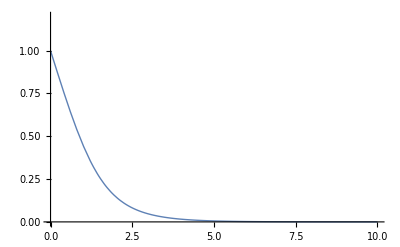

C:\Users\Oscar\Documents\GitHub\MasterThesisCode\data\N2XOR_AA_GenErr.txt

```mathematica
Eg:=-0.5D[Log[Zann], α]
Plot[Evaluate@Eg, {α, 0, 10}, PlotStyle->Thick, PlotRange -> {0, 1.2}]
data=Cases[Plot[Evaluate@Eg, {α, 0, 10},  PlotRange -> {0, 1.2}],Line[data_]:>data,-4,1][[1]];
Export["C:\Users\Oscar\Documents\GitHub\MasterThesisCode\data\N2XOR_AA_GenErr.txt",data,"Table"]
```